```mathematica
Clear["Global`*"]
```

# Differential equations

## Data:

Solve the model: diff eqn and boundary conditions:

```mathematica
mdl={deqn=-u''[x]==1+x,bnd1=u[0]==0,bnd2=u[1]==0};
```

```mathematica
$Assumptions=x>0;
```

## Solution:

Solve the eqn, object to the boundary conditions:

```mathematica
sln = DSolve[mdl,u[x],x]
```

{{u[x]→1/6 (4 x-3 x^2-x^3)}}

Extract u[x] from the sln list and assign it to the function u:

```mathematica
u[x_]=u[x]/.sln[[1]]//FullSimplify
```

-1/6 (-1+x) x (4+x)

Verify that u satisfies the diff eqn and boundary conditions:

```mathematica
deqn//FullSimplify
```

True

```mathematica
bnd1//FullSimplify
```

True

```mathematica
bnd2//FullSimplify
```

True

Find the roots of u(x):

```mathematica
Roots[u[x]==0, x]
```

x==1||x==0||x==-4

Find max and min:

```mathematica
FindMaximum[u[x],x]
```

{0.188075,{x→0.527525}}

```mathematica
FindMinimum[u[x],{x,0.5}]
```

{-2.18808,{x→-2.52753}}

Find limits:

```mathematica
Limit[u[x],x->0]
```

0

```mathematica
Limit[u[x],x->Infinity]
```

-∞

Plot the solution:

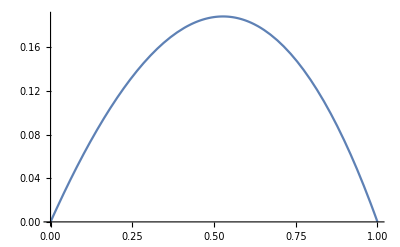

```mathematica
Plot[u[x],{x,0,1}]
```

End.